```mathematica
a=Import["~/ACS_LOG_2025-02-17_H16_M04_S15/ACS_LOG_2025-02-17_H16_M04_S15.csv","CSV"];
```

```mathematica
a[[1]]
```

{2025 Feb 17 16:04:15.438,0.01,200948.,20.1875,0.,0.,18.375,18.125,-12.5625,18.25,18.625,-15.1875,-15.0625,1}

```mathematica
Length[a[[1]]]
```

14

```mathematica
a[[Length[a]]]
```

{2025 Feb 19 12:34:51.792,160236.,200763.,18.9375,0.,0.,17.125,16.625,-13.6875,17.1875,17.125,-15.0625,-15.125,0}

```mathematica
b=Transpose[a];
```

```mathematica
c=Table[{b[[2,i]],b[[9,i]]},{i,Length[b[[2]]]}];
```

```mathematica
c[[1]]
```

{0.01,-12.5625}

```mathematica
ListPlot[c,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

-Graphics-

```mathematica
Length[b[[1]]]
```

273631

```mathematica
d=Table[{b[[2,i]],b[[14,i]]},{i,1,Length[b[[2]]],10}];
```

```mathematica
pc[x_]:=If[x==1,Red,Blue]
```

```mathematica
p=Table[Graphics[{pc[d[[i,2]]],Point[d[[i]]]}],{i,Length[d]}];
```

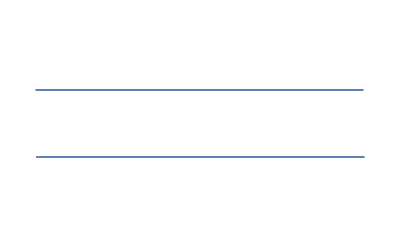

```mathematica
ListPlot[d,PlotRange->{-1,2},Axes->False]
```